```mathematica
Задаём значения констант
```

```mathematica
ϵ=10^(-3);znak=4;
```

```mathematica
Определяем необходимые функции
```

```mathematica
(*X0={-1,-2};α=1;f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2*)
```

```mathematica
X0={-2Sqrt[5],1};f[{x_,y_}]=6x^2+3y^2-4x y+4Sqrt[5](x+2y)+22;
```

```mathematica
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
```

```mathematica
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
```

```mathematica
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
Hesse[{x1_,y1_}]:=D[f[{x,y}],{{x,y},2}]/.{x->x1,y->y1}
```

```mathematica
Инициализируем переменные
```

```mathematica
X=X0;
points={X0};
norm={NormGradF[X0]};
ωArray={antiGradF[X0]};
κArray={};fValues={f[X0]};
γArray={};pArray={antiGradF[X0]};
i=0;k=1;
ifunk={i};
symi=0;
```

```mathematica
АЛГОРИТМ
```

```mathematica
While[norm[[-1]]≥ϵ,
i=0;
κArray=Append[κArray,NArgMin[f[X+κ pArray[[-1]]],κ,StepMonitor:>i++]];
X+=κArray[[-1]] pArray[[-1]];
points=Append[points,X];
fValues=Append[fValues,f[X]];i++;symi+=i; 
ifunk=Append[ifunk,i];
ωArray=Append[ωArray,antiGradF[X]];
norm=Append[norm,NormGradF[X]];
(*k mod 2 - момент рестарта, кратный размернойсти пространства*)
(*γArray=Append[γArray,norm[[-1]]^2/norm[[-2]]^2 Mod[k,2]](*Метод Флетчера-Ривса*);*)
(*γArray=Append[γArray,((ωArray[[-1]]-ωArray[[-2]]).ωArray[[-1]])/norm[[-2]]^2 Mod[k,2]];(*Метод Полака-Рибьера*)*)
γArray=Append[γArray,-((Hesse[X].pArray[[-1]]).ωArray[[-1]])/((Hesse[X].pArray[[-1]]).pArray[[-1]])Mod[k,2]];(*Метод Q=H(X^k)*)
pArray=Append[pArray,γArray[[-1]]pArray[[-1]]+ωArray[[-1]]]; k++
];"Результат получен за "<>ToString[Length[points]-1]<> " итер. Точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>". Функция f(x) в алгоритме была вычислена "<>ToString[symi]<>" раз."
```

Результат получен за 2 итер. Точка минимума X = {-2.236, -4.472}. Функция f(x) в алгоритме была вычислена 119 раз.

```mathematica
SetAccuracy[f[X],znak]" - минимум функции f(X)"
```

-28.  - минимум функции f(X)

```mathematica
АНАЛИЗ РЕЗУЛЬТАТОВ ВЫЧИСЛИТЕЛЬНОГО ЭКСПЕРИМЕНТА
2. Траектория поиска точки минимума
```

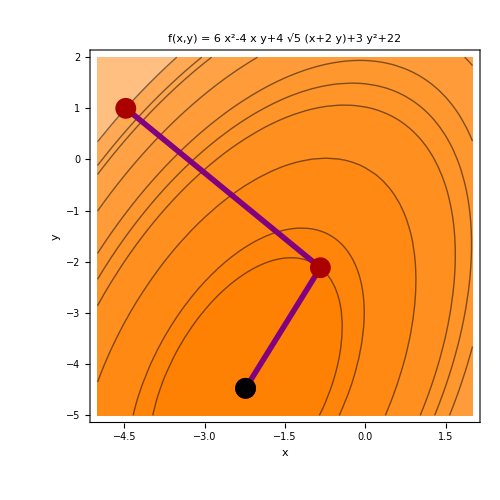

```mathematica
CP0={-5,-5}; CP1={2,2}; a:=1;b:=2;
(*Метод Флетчера-Ривса*)
(*CP0={-5,-5}; CP1={2,2}; a:=1;b:=2; Квадратичная функция*) 
(*CP0={-2,-2.5}; CP1={2,1.5}; a:=8;b:=9; функция Розенброка при лямда=1*)
(*CP0={-2,-2.5}; CP1={2,1.5}; a:=8;b:=12; функция Розенброка при лямда=50*)
(*CP0={-11.5,-2.5}; CP1={11.5,20.5}; a:=8;b:=20; функция Розенброка при лямда=1000*)
(*Метод Полака-Рибьера*)
(*CP0={-2,-2.5}; CP1={2,1.5}; a:=7;b:=8; функция Розенброка при лямда=1*)
(*CP0={-2,-2.5}; CP1={2,1.5}; a:=8;b:=12; функция Розенброка при лямда=50*)
(*CP0={-13,-2.5}; CP1={13,23.5}; a:=8;b:=20; функция Розенброка при лямда=1000*)
(*Метод Q=H(X^k)*)
(*CP0={-2,-2.5}; CP1={2,1.5}; a:=8;b:=12; функция Розенброка при лямда=50*)
ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}]
```

```mathematica
3. Анализ сходимости метода: убывание нормы невязки
```

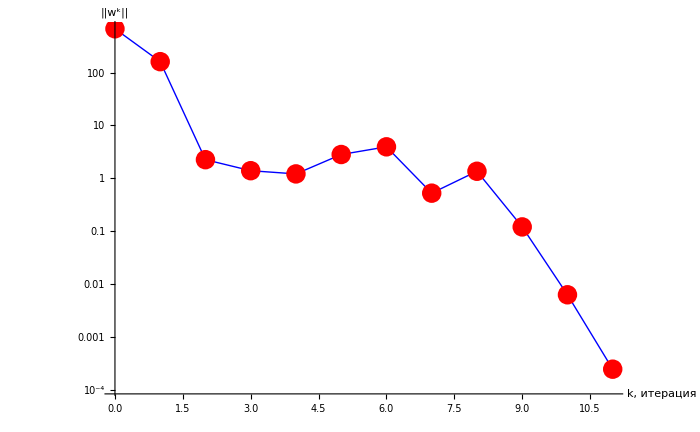

```mathematica
ListLogPlot[norm,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,DataRange->{0,Length[points]-1},MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
4. Таблицы
```

```mathematica
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||","i"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],znak]]<>", "<>ToString[SetAccuracy[points[[i,2]],znak]]<>" )"]
gridData[[All,3]]=SetAccuracy[fValues,znak];
gridData[[All,4]]={"-"}~Join~SetAccuracy[κArray,znak];
gridData[[All,5]]=SetAccuracy[norm,znak];
gridData[[All,6]]=ifunk;
gridData={gridLabel}~Join~gridData;
```

```mathematica
If[Length[points]>20,Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[Length[points]-4;;Length[points]+1]],Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]],Grid[gridData[[1;;Length[points]]]~Join~gridData[[Length[points]-4;;Length[points]+1]],Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]]
```

k | X^k | f(X^k) | κ_k | ||w^k|| | i
0 | ( -1.000, -2.000 ) | 454. | - | 674.4 | 0
1 | ( 0.254, -1.377 ) | 104.477 | 0.002 | 160.97 | 64
2 | ( -0.064,       -3
-0. 10 ) | 1.133 | 0.009 | 2.25 | 73
3 | ( 0.589, 0.334 ) | 0.177 | 0.316 | 1.392 | 65
4 | ( 0.595, 0.357 ) | 0.165 | 0.012 | 1.21 | 65
5 | ( 0.733, 0.518 ) | 0.088 | 0.077 | 2.818 | 65
6 | ( 0.849, 0.699 ) | 0.046 | 0.01 | 3.939 | 55
7 | ( 0.859, 0.739 ) | 0.02 | 0.003 | 0.523 | 65
8 | ( 0.936, 0.870 ) | 0.006 | 0.081 | 1.358 | 55
... | ... | ... | ... | ... | ...
6 | ( 0.849, 0.699 ) | 0.046 | 0.01 | 3.939 | 55
7 | ( 0.859, 0.739 ) | 0.02 | 0.003 | 0.523 | 65
8 | ( 0.936, 0.870 ) | 0.006 | 0.081 | 1.358 | 55
9 | ( 1.001, 1.001 ) | 0. | 0.008 | 0.12 | 55
10 | ( 0.999, 0.999 ) | 0. | 0.002 | 0.006 | 65
11 | ( 1.00, 1.00 ) | 0. | 0.018 | 0.0002 | 53

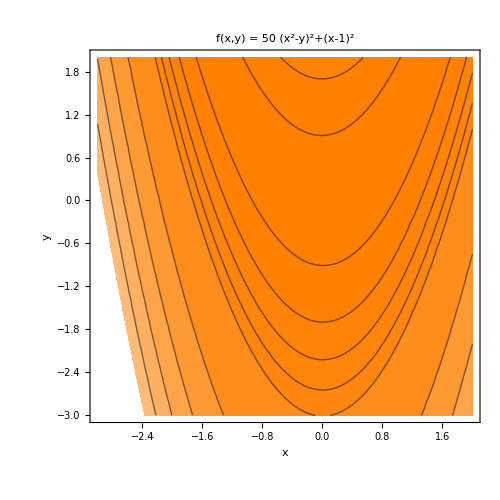

```mathematica
ContourPlot[f[{x,y}],{x,Min[points]-1,Max[points]+1},{y,Min[points]-1,Max[points]+1},Contours->uniformMesh[Max[f[{Min[points]-1,Min[points]-1}],f[{Min[points]-1,Max[points]+1}],f[{Max[points]+1,Min[points]-1}],f[{Max[points]+1,Max[points]+1}]],fValues[[1]],10]~Join~uniformMesh[fValues[[1]],0.4 (fValues[[2]]+fValues[[3]]),4],ColorFunction->(If[#<0,Darker[Blue,Abs[0.5 #]],Lighter[Orange,0.5 #]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500]
```